```mathematica
comment[c_,val_]:=Module[{}, Print[c]; val];
```

```mathematica
ClearAll[m0];ClearAll[Γ0];ClearAll[S];ClearAll[L0];ClearAll[decays];

(** Nucleons **)
m0[p938]=0.938;Γ0[p938]=0.;S[p938]=1/2;L0[p938]=0;

m0[p1440]=1.440;Γ0[p1440]=0.200;S[p1440]=1/2;L0[p1440]=0;
decays[p1440]={
{{p938,pi},0.70},
{{p938,pipi},0.05},
{{Δ1232,pi},0.25}
};

m0[p1520]=1.520;Γ0[p1520]=0.125;S[p1520]=3/2;L0[p1520]=1;
decays[p1520]={
{{p938,pi},0.60},
{{p938,pipi},0.15},
{{Δ1232,pi},0.25}
};

m0[p1535]=1.535;Γ0[p1535]=0.150;S[p1535]=1/2;L0[p1535]=1;
decays[p1535]={
{{p938,gamma},0.001},
{{p938,pi},0.549},
{{p938,eta},0.35},
{{p938,pipi},0.05},
{{p1440,pi},0.05}
};

m0[p1650]=1.650;Γ0[p1650]=0.150;S[p1650]=1/2;L0[p1650]=1;
decays[p1650]={
{{p938,pi},0.65},
{{p938,eta},0.05},
{{p938,pipi},0.05},
{{Δ1232,pi},0.10},
{{p1440,pi},0.05},
{{Lambda,Ka},0.10}
};

m0[p1675]=1.675;Γ0[p1675]=0.140;S[p1675]=5/2;L0[p1675]=1;
decays[p1675]={
{{p938,pi},0.45},
{{Δ1232,pi},0.55}
};

m0[p1680]=1.680;Γ0[p1680]=0.120;S[p1680]=5/2;L0[p1680]=2;
decays[p1680]={
{{p938,pi},0.65},
{{p938,pipi},0.20},
{{Δ1232,pi},0.15}
};

m0[p1700]=1.700;Γ0[p1700]=0.100;S[p1700]=3/2;L0[p1700]=1;
decays[p1700]={
{{p938,pi},0.10},
{{p938,eta},0.05},
{{p938,rho},0.05},
{{p938,pipi},0.45},
{{Δ1232,pi},0.35}
};

m0[p1710]=1.710;Γ0[p1710]=0.110;S[p1710]=1/2;L0[p1710]=0;
decays[p1710]={
{{p938,pi},0.15},
{{p938,eta},0.20},
{{p938,rho},0.05},
{{p938,pipi},0.20},
{{Δ1232,pi},0.20},
{{p1440,pi},0.10},
{{Lambda,Ka},0.10}
};

m0[p1720]=1.720;Γ0[p1720]=0.150;S[p1720]=3/2;L0[p1720]=2;
decays[p1720]={
{{p938,pi},0.15},
{{p938,rho},0.25},
{{p938,pipi},0.45},
{{Δ1232,pi},0.10},
{{Lambda,Ka},0.05}
};

(*1900*)

(*1990*)

(*2080*)

m0[p2190]=2.190;Γ0[p2190]=0.550;S[p2190]=7/2;L0[p2190]=3;
decays[p2190]={
{{p938,pi},0.35},
{{p938,rho},0.30},
{{p938,pipi},0.15},
{{Δ1232,pi},0.15},
{{p1440,pi},0.05}
};

m0[p2220]=2.220;Γ0[p2220]=0.550;S[p2220]=9/2;L0[p2220]=4;
decays[p2220]={
{{p938,pi},0.35},
{{p938,rho},0.25},
{{p938,pipi},0.20},
{{Δ1232,pi},0.20}
};

m0[p2250]=2.250;Γ0[p2250]=0.470;S[p2250]=9/2;L0[p2250]=3;
decays[p2250]={
{{p938,pi},0.30},
{{p938,rho},0.25},
{{p938,pipi},0.20},
{{Δ1232,pi},0.20},
{{p1440,pi},0.05}
};

ps={p1440,p1520,p1535,p1650,p1675,p1680,p1700,p1710,p1720,p2190,p2220,p2250};



(** Delta particles **)
m0[Δ1232]=1.232;Γ0[Δ1232]=0.115;S[Δ1232]=3/2;L0[Δ1232]=0;
decays[Δ1232]={
{{p938,gamma}, 0.01},
{{p938,pi},0.99}
};

m0[Δ1600]=1.700;Γ0[Δ1600]=0.200;S[Δ1600]=3/2;L0[Δ1600]=0;
decays[Δ1600]={
{{p938,pi},0.15},
{{Δ1232,pi},0.55},
{{p1440,pi},0.30}
};

m0[Δ1620]=1.675;Γ0[Δ1620]=0.180;S[Δ1620]=1/2;L0[Δ1620]=0;
decays[Δ1620]={
{{p938,pi},0.25},
{{Δ1232,pi},0.60},
{{p1440,pi},0.15}
};

m0[Δ1700]=1.750;Γ0[Δ1700]=0.300;S[Δ1700]=3/2;L0[Δ1700]=1;
decays[Δ1700]={
{{p938,pi},0.20},
{{p938,rho},0.10},
{{Δ1232,pi},0.55},
{{p1440,pi},0.15}
};

(*(*1900*)m0[Δ[4]]=1.850;Γ0[Δ[4]]=0.240;S[Δ[4]]=1/2;*)

m0[Δ1905]=1.880;Γ0[Δ1905]=0.280;S[Δ1905]=5/2;L0[Δ1905]=2;
decays[Δ1905]={
{{p938,pi},0.20},
{{p938,rho},0.60},
{{Δ1232,pi},0.10},
{{p1440,pi},0.10}
};

m0[Δ1910]=1.900;Γ0[Δ1910]=0.250;S[Δ1910]=1/2;L0[Δ1910]=2;
decays[Δ1910]={
{{p938,pi},0.35},
{{p938,rho},0.40},
{{Δ1232,pi},0.15},
{{p1440,pi},0.10}
};

m0[Δ1920]=1.920;Γ0[Δ1920]=0.150;S[Δ1920]=3/2;L0[Δ1920]=2;
decays[Δ1920]={
{{p938,pi},0.15},
{{p938,rho},0.30},
{{Δ1232,pi},0.30},
{{p1440,pi},0.25}
};

(*(*1930*)m0[Δ[8]]=1.930;Γ0[Δ[8]]=0.250;S[Δ[8]]=5/2;*)

m0[Δ1950]=1.950;Γ0[Δ1950]=0.250;S[Δ1950]=7/2;L0[Δ1950]=2;
decays[Δ1950]={
{{p938,gamma},0.01},
{{p938,pi},0.44},
{{p938,rho},0.15},
{{Δ1232,pi},0.20},
{{p1440,pi},0.20}
};

Δs={Δ1600,Δ1620,Δ1700, Δ1905,Δ1910,Δ1920,Δ1950};


(*Decay products*)
m0[pi]=0.137;Γ0[pi]=0.;S[pi]=1/2;
m0[gamma]=0.;Γ0[gamma]=0.;S[gamma]=1;
m0[pipi]=2m0[pi];Γ0[pipi]=0.;S[pipi]=1;
m0[eta]=0.548;Γ0[eta]=0.;S[eta]=1;
m0[rho]=0.775;Γ0[rho]=0.149;S[rho]=1;
decays[rho]={
{{pi,pi},1.}
};
m0[Lambda]=1.116;Γ0[Lambda]=0.;S[Lambda]=1/2;
m0[Ka]=0.498;Γ0[Ka]=0.;S[Ka]=0;

decays[p_]:=Throw["No decays found for "<>ToString[p]];
m0[p_]:=Throw["No nominal mass found for "<>ToString[p]];
Γ0[p_]:=Throw["No nominal width found for "<>ToString[p]];
S[p_]:=Throw["No spin found for "<>ToString[p]];
L0[p_]:=Throw["No orbital angular momentum found for "<>ToString[p]];


(* Define the width function Γ *)
ClearAll[BR]; ClearAll[massDecayBound];
BR[particle_,outs_]:=Select[decays[particle],#[[1]]==outs&,1][[1,2]];
Γ0[hIn_,hOuts_]:=Γ0[hIn] BR[hIn,hOuts];
minMass[particle_]:=If[Γ0[particle]==0.,m0[particle],0.];
massDecayBound[particle_]:=massDecayBound[particle]=
Min[(Total[minMass/@First[#]]&) /@ decays[particle]];

pCMS[eCM_,mA_,mB_]:=If[eCM≤mA+mB,0.,1/(2.eCM)*Sqrt[(eCM^2-(mA+mB)^2)(eCM^2-(mA-mB)^2)]];
psSize[mDistribution_][eCM_,{hA_,hB_}]:=Module[{m0A,m0B},m0A=m0[hA];m0B=m0[hB];
If[Γ0[hA]==Γ0[hB]==0.,
If[eCM<m0A+m0B,Return[0],Return@pCMS[eCM,m0A,m0B]]
];
If[Γ0[hA]==0.,
If[eCM<m0A,Return[0],
Return@NIntegrate[pCMS[eCM,m0A,mB]mDistribution[hB,mB],{mB,massDecayBound[hB],eCM-m0A}, PrecisionGoal->3]
]];
If[Γ0[hB]==0.,
If[eCM<m0B,Return[0],
Return@NIntegrate[pCMS[eCM,mA,m0B]mDistribution[hA,mA],{mA,massDecayBound[hA],eCM-m0B}, PrecisionGoal->3]
]];
NIntegrate[pCMS[eCM,mA,mB]mDistribution[hA,mA]mDistribution[hB,mB],{mA,massDecayBound[hA],eCM},{mB,massDecayBound[hB],eCM-mA}, PrecisionGoal->3]
];

ClearAll[a0];
breitWigner[Γ0_,m0_Real,m_Real]:=Γ0/((m0-m)^2+Γ0^2/4)
a0[particle_,m_Real]:=If[Γ0[particle]==0.,Throw["In a0: Singular mass distribution for "<>ToString[particle]],
breitWigner[Γ0[particle],m0[particle],m]/(2Pi)
];
p0Mean=psSize[a0];
ClearAll[p0MeanCh];
p0MeanCh[m0_,hA_,hB_]:=p0MeanCh[m0,hA,hB]=p0Mean[m0,hA,hB];

ClearAll[Γ];
Γ[hIn_,hOuts_,m_Real]:= Module[{p0,p0res},
p0=p0Mean[m,hOuts[[1]],hOuts[[2]]];
p0res= p0MeanCh[m0[hIn],hOuts[[1]],hOuts[[2]]];
If[p0res==0,Throw["Mean p at resonance is zero for "<>ToString[hIn]<>"-->"<>ToString[hOuts]]];
If[p0==0,Return[0]];
Γ0[hIn,hOuts] * m0[hIn]/m * (p0/p0res)^(2L0[hIn]+1) * 1.2/(1. + 0.2(p0/p0res)^(2L0[hIn]))
];
Γ[h_,m_]:=Sum[Γ[h,decs[[1]],m],{decs,decays[h]}];


(* Define the mass distribution function and <p> *)
ClearAll[aN]; ClearAll[a];
aN[particle_]:=comment["Calculating aN for "<>ToString[particle],
aN[particle]=Re@NIntegrate[Γ[particle,m]/((m0[particle]-m)^2+Γ[particle,m]^2/4),{m,mBound,Infinity}]
];

a[particle_,m_Real]:=If[Γ0[particle]==0.,Throw["In a: Singular mass distribution for "<>ToString[particle]],
breitWigner[Γ[particle,m],m0[particle],m]/aN[particle]
];
pMean=psSize[a];


(* Matrix elements and cross-sections *)
ClearAll[matrixElement];ClearAll[meA];
matrixElement[eCM_,{p938,Δ1232},mA_,mB_]:=40000 * (m0[Δ1232] Γ0[Δ1232])^2/((eCM^2 -m0[Δ1232]^2)^2 +( m0[Δ1232] Γ0[Δ1232])^2);
matrixElement[eCM_,{Δ1232,Δ1232},mA_,mB_]:=2.8;
meA[p938,h_]:=If[MemberQ[ps,h],6.3,12.0];
meA[Δ1232,h_]:=3.5;
matrixElement[eCM_,{hA_,hB_},mA_,mB_]:=meA[hA,hB]/((mB-mA)^2(mB+mA)^2);

ClearAll[sigmapp];
sigmapp[eCM_,{hA_,hB_}]:=If[eCM≤2m0[p938],0,
(2S[hA]+1)(2S[hB]+1) * pMean[eCM,hA,hB]/pMean[eCM,p938,p938] * matrixElement[eCM,{hA,hB},m0[hA],m0[hB]]/eCM^2
];
```

```mathematica
ptspΔ=Monitor[
Table[{eCM,sigmapp[eCM,{p938,Δ1232}]},{eCM,2.,8.,0.01}],
{ProgressIndicator[eCM,{2.,8.}],eCM}
];
```

```mathematica
ptsΔΔ=Monitor[
Table[{eCM,sigmapp[eCM,{Δ1232,Δ1232}]},{eCM,2.,8.,0.05}],
{ProgressIndicator[eCM,{2.,8.}],eCM}
];
```

```mathematica
ptspΔstar=Monitor[
Table[{eCM,Sum[sigmapp[eCM,{p938,Δ}],{Δ,Δs}]},{eCM,2.,8.,0.1}],
{Δ,ProgressIndicator[eCM,{2.,8.}],eCM}
];
```

Calculating aN for Δ1600

Calculating aN for Δ1620

Calculating aN for Δ1700

Calculating aN for Δ1905

Calculating aN for Δ1910

Calculating aN for Δ1920

Calculating aN for Δ1950

```mathematica
ptsppstar = Monitor[
Table[{eCM,Sum[sigmapp[eCM,{p938,p}],{p,ps}]},{eCM,2.,8.,0.1}],
{p,ProgressIndicator[eCM,{2.,8.}],eCM}
];
```

Calculating aN for p1440

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Calculating aN for p1520

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

Calculating aN for p1535

Calculating aN for p1650

Calculating aN for p1675

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

Calculating aN for p1680

Calculating aN for p1700

Calculating aN for p1710

Calculating aN for p1720

Calculating aN for p2190

Calculating aN for p2220

Calculating aN for p2250

```mathematica
ptsΔpstar=Monitor[
Table[{eCM,Sum[sigmapp[eCM,{Δ1232,p}],{p,ps}]},{eCM,2.,8.,0.1}],
{p,ProgressIndicator[eCM,{2.,8.}],eCM}
];
```

Calculating aN for Δ1232

NIntegrate::izero: Integral and error estimates are 0 on all integration subregions. Try increasing the value of the MinRecursion option. If value of integral may be 0, specify a finite value for the AccuracyGoal option.

General::stop: Further output of NIntegrate::izero will be suppressed during this calculation.

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

```mathematica
ptsΔΔstar=Monitor[
Table[{eCM,Sum[sigmapp[eCM,{Δ1232,Δ}],{Δ,Δs}]},{eCM,2.,8.,0.1}],
{Δ,ProgressIndicator[eCM,{2.,8.}],eCM}
];
```

Calculating aN for Δ1600

Calculating aN for Δ1620

Calculating aN for Δ1700

Calculating aN for Δ1905

Calculating aN for Δ1910

Calculating aN for Δ1920

Calculating aN for Δ1950

NIntegrate::slwcon: Numerical integration converging too slowly; suspect one of the following: singularity, value of the integration is 0, highly oscillatory integrand, or WorkingPrecision too small.

General::stop: Further output of NIntegrate::slwcon will be suppressed during this calculation.

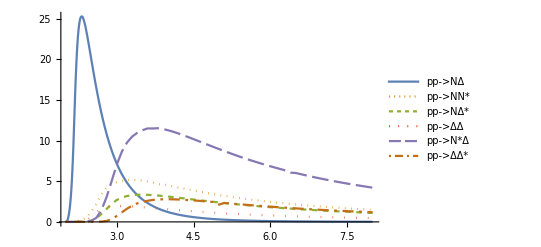

```mathematica
ListLinePlot[MulY[12./17.]/@{ptspΔ,ptsppstar,ptspΔstar,ptsΔΔ,ptsΔpstar,ptsΔΔstar},
PlotStyle->{Automatic,Dashing[{0.001,0.01}],Dashing[{0.01,0.01}],Dashing[{0.001,0.02}],Dashing[{0.03,0.01}],Dashing[{0.005,0.01,0.02,0.01}]},
PlotRange->All,PlotLegends->{"pp->NΔ","pp->NN*","pp->NΔ*","pp->ΔΔ","pp->N*Δ","pp->ΔΔ*"} 
]
```

```mathematica
ScaleY[fac_][lst_]:=Table[{p[[1]],fac p[[2]]},{p,lst}];
```